```mathematica
bodyA=Import[FileNameJoin[{NotebookDirectory[],"bodyA.dat"}],"csv"];
bodyB=Import[FileNameJoin[{NotebookDirectory[],"bodyB.dat"}],"csv"];
bodyC=Import[FileNameJoin[{NotebookDirectory[],"bodyC.dat"}],"csv"];
Print["1行目 : ",bodyA[[1]]]
```

1行目 : {# t,x,y,z,qx,qy,qz}

```mathematica
{tA,xA,yA,zA,qxA,qyA,qzA}=Transpose[bodyA[[2;;]]];
{tB,xB,yB,zB,qxB,qyB,qzB}=Transpose[bodyB[[2;;]]];
{tC,xC,yC,zC,qxC,qyC,qzC}=Transpose[bodyC[[2;;]]];
```

```mathematica
xyzA=Transpose[{xA,yA,zA}];
xyzB=Transpose[{xB,yB,zB}];
xyzC=Transpose[{xC,yC,zC}];
```

```mathematica
Manipulate[
Graphics3D[{Line[Table[{xyzA[[i]],xyzB[[i]],xyzC[[i]]},{i,1,max}]]},
BoxRatios->{1, 1, 1}]
,{max,1,Length[xyz]}]
```

```mathematica
(*繰り返し使うプロット用オプション*)
plotopt={
PlotRange->All,
Joined->True,
GridLines->All,
Frame->True,
FrameStyle->Directive@{Black,FontSize->18},
BaseStyle->{FontFamily->"Times New Roman"}};
```

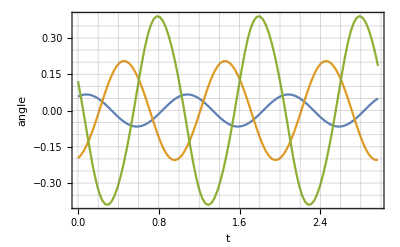

```mathematica
figOriginal=ListPlot[{
Transpose@{tA,qzA},
Transpose@{tB,qzB},
Transpose@{tC,qzC}},
FrameLabel->{HoldForm[t],"angle"},
Evaluate[plotopt]]
```

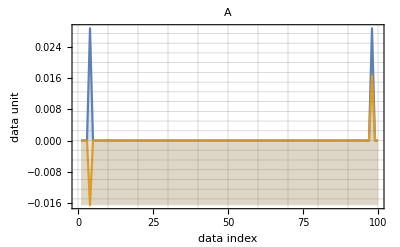

```mathematica
cnA=Fourier[qzA,FourierParameters->{-1, -1}];
ListPlot[{Re@cnA,Im@cnA},
FrameLabel->{"data index","data unit"},
PlotLabel->"A",
Filling->Bottom,
Evaluate[plotopt]]
```

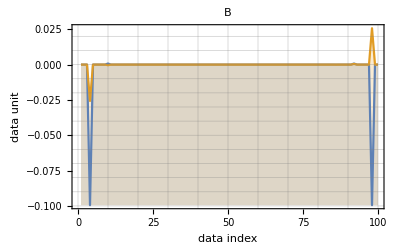

```mathematica
cnB=Fourier[qzB,FourierParameters->{-1, -1}];
ListPlot[{Re@cnB,Im@cnB},
FrameLabel->{"data index","data unit"},
PlotLabel->"B",
Filling->Bottom,
Evaluate[plotopt]]
```

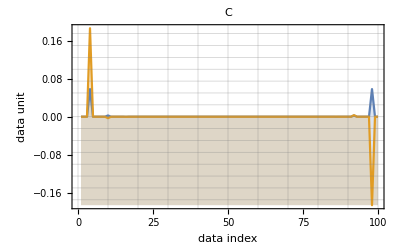

```mathematica
cnC=Fourier[qzC,FourierParameters->{-1, -1}];
ListPlot[{Re@cnC,Im@cnC},
FrameLabel->{"data index","data unit"},
PlotLabel->"C",
Filling->Bottom,
Evaluate[plotopt]]
```

```mathematica
(*cnの半分はマイナスの周波数の係数として使う．*)
index[n_]:=If[n<0,n,n+1];
```

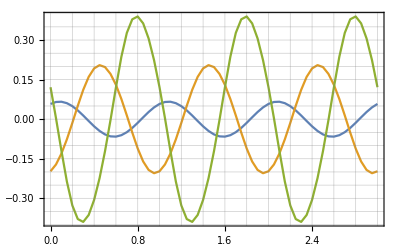

```mathematica
f[cn_,t_,T_]:=With[{len=Length[cn]},Sum[cn[[index[n]]]*Exp[I*n*2 π/T*t],{n,-Floor[len/2],Floor[len/2],1}]];
figInvFourier=ListPlot[{
Table[{t,Re[f[cnA,t,3]]},{t,0,3.,0.05}],
Table[{t,Re[f[cnB,t,3]]},{t,0,3.,0.05}],
Table[{t,Re[f[cnC,t,3]]},{t,0,3.,0.05}]},
Joined->True,
Evaluate[plotopt]]
```